```mathematica
Quit[]
```

Routines for YODA plotting

from: https://yoda.hepforge.org/trac/wiki/DataFormat

```mathematica
<<(NotebookDirectory[]<>"../../atom_mathematica.m")
```

```mathematica
WW=GetYodaRaw[NotebookDirectory[]<>"WW.yoda"];
WWmg5=GetYodaRaw[NotebookDirectory[]<>"WW_mg5.yoda"];
WWjmg5=GetYodaRaw[NotebookDirectory[]<>"WWj_mg5.yoda"];
ATLASwwe=GetYodaRaw[NotebookDirectory[]<>"WW_en.yoda"];
ATLASwwm=GetYodaRaw[NotebookDirectory[]<>"WW_mn.yoda"];
```

1 Imported ..Histo1D..  /ATLAS_1410_7238/Mjj/0

2 Imported ..Histo1D..  /ATLAS_1410_7238/R_pT/0

1 Imported ..Histo1D..  /ATLAS_1410_7238/Mjj/0

2 Imported ..Histo1D..  /ATLAS_1410_7238/R_pT/0

1 Imported ..Histo1D..  /ATLAS_1410_7238/Mjj/0

2 Imported ..Histo1D..  /ATLAS_1410_7238/R_pT/0

1 Imported ..Scatter2D..  /REF/d01-x01-y01

1 Imported ..Scatter2D..  /REF/d01-x01-y01

This contains Hist1D objects:

Rescaling Histogram y-Axis with 0.48

Rescaling Histogram y-Axis with 1.48

Rescaling Histogram y-Axis with 3.5

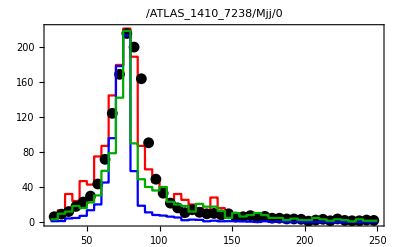

```mathematica
Fig1=HistogramPlot[WW[[1]],HistStyle->{Red},HistScale->0.48];
Figmg5=HistogramPlot[WWmg5[[1]],HistStyle->{Blue},HistScale->1.48];
Figmg5j=HistogramPlot[WWjmg5[[1]],HistStyle->{Darker[Green]},HistScale->3.5];
Fig2=ScatterPlot[ATLASwwe[[1]],PlotStyle->{Black}];
Show[{Fig1,Fig2,Figmg5,Figmg5j}]
```

Rescaling Histogram y-Axis with 0.53

Rescaling Histogram y-Axis with 1.7

Rescaling Histogram y-Axis with 4.

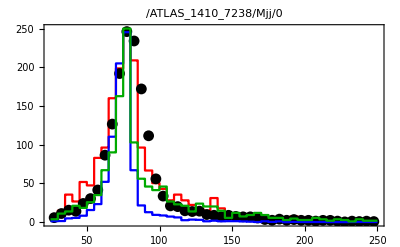

```mathematica
Fig1=HistogramPlot[WW[[1]],HistStyle->{Red},HistScale->0.53];
Fig2=ScatterPlot[ATLASwwm[[1]],PlotStyle->{Black}];
Figmg5=HistogramPlot[WWmg5[[1]],HistStyle->{Blue},HistScale->1.7];
Figmg5j=HistogramPlot[WWjmg5[[1]],HistStyle->{Darker[Green]},HistScale->4.0];
Show[{Fig1,Fig2,Figmg5,Figmg5j}]
```

Smearing OFF

```mathematica
WW=GetYodaRaw[NotebookDirectory[]<>"WW_off.yoda"];
WWmg5=GetYodaRaw[NotebookDirectory[]<>"WW_mg5_off.yoda"];
WWjmg5=GetYodaRaw[NotebookDirectory[]<>"WWj_mg5_off.yoda"];
ATLASwwe=GetYodaRaw[NotebookDirectory[]<>"WW_en.yoda"];
ATLASwwm=GetYodaRaw[NotebookDirectory[]<>"WW_mn.yoda"];
```

1 Imported ..Histo1D..  /ATLAS_1410_7238/Mjj/0

2 Imported ..Histo1D..  /ATLAS_1410_7238/R_pT/0

1 Imported ..Histo1D..  /ATLAS_1410_7238/Mjj/0

2 Imported ..Histo1D..  /ATLAS_1410_7238/R_pT/0

1 Imported ..Histo1D..  /ATLAS_1410_7238/Mjj/0

2 Imported ..Histo1D..  /ATLAS_1410_7238/R_pT/0

1 Imported ..Scatter2D..  /REF/d01-x01-y01

1 Imported ..Scatter2D..  /REF/d01-x01-y01

This contains Hist1D objects:

Rescaling Histogram y-Axis with 0.48

Rescaling Histogram y-Axis with 1.48

Rescaling Histogram y-Axis with 3.5

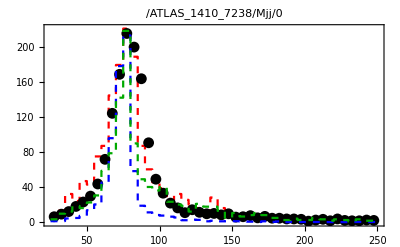

```mathematica
Fig1off=HistogramPlot[WW[[1]],HistStyle->{Red,Dashed},HistScale->0.48];
Figmg5off=HistogramPlot[WWmg5[[1]],HistStyle->{Blue,Dashed},HistScale->1.48];
Figmg5joff=HistogramPlot[WWjmg5[[1]],HistStyle->{Darker[Green],Dashed},HistScale->3.5];
Fig2off=ScatterPlot[ATLASwwe[[1]],PlotStyle->{Black}];
Show[{Fig1off,Fig2off,Figmg5off,Figmg5joff}]
```

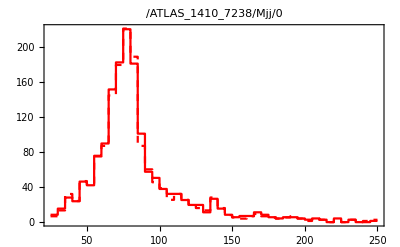

```mathematica
Show[{Fig1off,Fig1}]
```

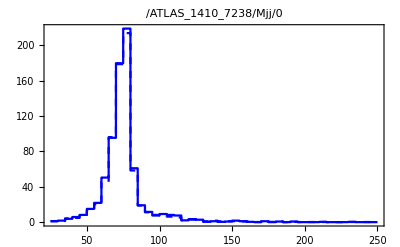

```mathematica
Show[{Figmg5off,Figmg5}]
```

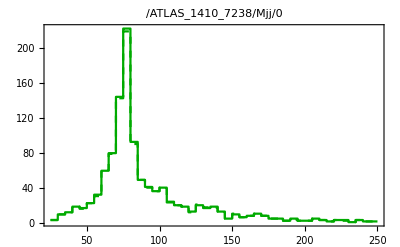

```mathematica
Show[{Figmg5joff,Figmg5j}]
```